```mathematica
(*(-(2*0.01)^2*(0.939)^2+(1-(0.01)^2))^(1/2)
(-(2*0.001)^2*(0.939)^2+(1-(0.01)^2))^(1/2)
(-(2*0.0001)^2*(0.939)^2+(1-(0.01)^2))^(1/2)
(-(2*0.00001)^2*(0.939)^2+(1-(0.01)^2))^(1/2)*)
```

```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-m-t.wdx"];
f1=Query[1,1]@a;
```

```mathematica
nf1=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Q->1,q3->0.97710345,Λ->1}];
ref1[x_]=Simplify[nf1/.{y->x}];
inf1[x_]=Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];

nf2=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.01,Q->1,q3->0.999773630178352,Λ->1}];
ref2[x_]=Simplify[nf2/.{y->x}];
inf2[x_]=Hold[NIntegrate[ref2[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];

nf3=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.001,Q->1,q3->0.9999482352182038,Λ->1}];
ref3[x_]=Simplify[nf3/.{y->x}];
inf3[x_]=Hold[NIntegrate[ref3[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];

nf4=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.0001,Q->1,q3->0.9999499811146356,Λ->1}];
ref4[x_]=Simplify[nf4/.{y->x}];
inf4[x_]=Hold[NIntegrate[ref4[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];

nf5=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.00001,Q->1,q3->0.9999499985735845,Λ->1}];
ref5[x_]=Simplify[nf5/.{y->x}];
inf5[x_]=Hold[NIntegrate[ref5[x],{k3,0,∞},{θ,0,2π},MaxRecursion->20]];
```

```mathematica
lf1=Table[{x,ReleaseHold[inf1[x]]},{x,-0.1,0.1,0.001}];
lf2=Table[{x,ReleaseHold[inf2[x]]},{x,-0.01,0.01,0.0001}];
lf3=Table[{x,ReleaseHold[inf3[x]]},{x,-0.001,0.001,0.00001}];
lf4=Table[{x,ReleaseHold[inf4[x]]},{x,-0.0001,0.0001,0.000001}];
lf5=Table[{x,ReleaseHold[inf5[x]]},{x,-0.00001,0.00001,0.0000001}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: (-1.35525×10^-20)^16 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.35525×10^-20)^17 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.35525×10^-20)^18 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::munfl: (-1.69407×10^-21)^15 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.69407×10^-21)^16 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.69407×10^-21)^17 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

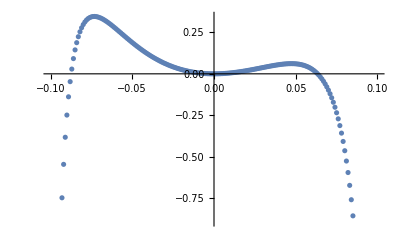

```mathematica
ListPlot[lf1]
```

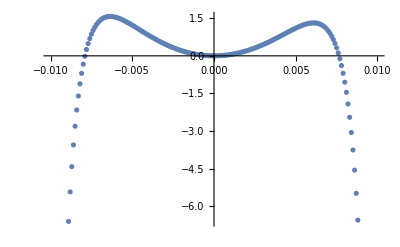

```mathematica
ListPlot[lf2]
```

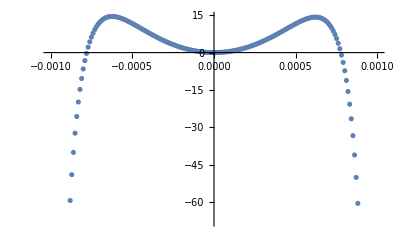

```mathematica
ListPlot[lf3]
```

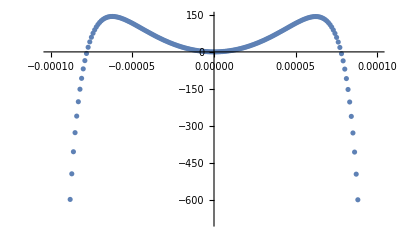

```mathematica
ListPlot[lf4]
```

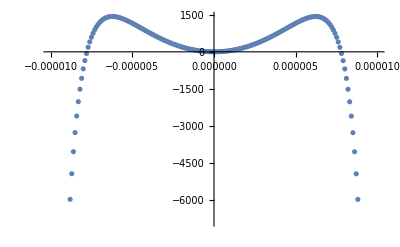

```mathematica
ListPlot[lf5]
```

```mathematica
nf1=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Q->1,q3->0.97710345,Λ->1}];

nf2=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.01,Q->1,q3->0.999773630178352,Λ->1}];

nf3=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.001,Q->1,q3->0.9999482352182038,Λ->1}];

nf4=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.0001,Q->1,q3->0.9999499811146356,Λ->1}];

nf5=Simplify[I*y*f1/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.00001,Q->1,q3->0.9999499985735845,Λ->1}];
```

```mathematica
ref1=NIntegrate[nf1,{y,-0.1,0.1},{k3,0,∞},{θ,0,2π},MaxRecursion->20];
ref2=NIntegrate[nf2,{y,-0.01,0.01},{k3,0,∞},{θ,0,2π},MaxRecursion->20];
ref3=NIntegrate[nf3,{y,-0.001,0.001},{k3,0,∞},{θ,0,2π},MaxRecursion->20];
ref4=NIntegrate[nf4,{y,-0.0001,0.0001},{k3,0,∞},{θ,0,2π},MaxRecursion->20];
ref5=NIntegrate[nf5,{y,-0.00001,0.00001},{k3,0,∞},{θ,0,2π},MaxRecursion->20];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ref1
```

-0.0520981

```mathematica
ref2
```

-0.0507114

```mathematica
ref3
```

-0.0507043

```mathematica
ref4
```

-0.0507043

```mathematica
ref5
```

-0.0507043